## Data:

### data save protocol:

```mathematica
SaveToCell::usage="SaveToCell[variable] creates an input cell that reassigns the current value of variable.\n"<>"SaveToCell[variables, display] shows 'display' on the right-hand-side of the assignment.";

SetAttributes[SaveToCell,HoldFirst]
SaveToCell[var_,name:Except[_?OptionQ]:"data",opt:OptionsPattern[]]:=With[{data=Compress[var],panel=ToBoxes@Tooltip[Panel[name,FrameMargins->Small],DateString[]]},CellPrint@Cell[BoxData@RowBox[{MakeBoxes[var],"=",InterpretationBox[panel,Uncompress[data]],";"}],"Input",(*prevent deletion by Cell>Delete All Output:*)GeneratedCell->False,(*CellLabel is special:last occrrence takes precedence,so it comes before opt:*)CellLabel->"(saved)",opt,CellLabelAutoDelete->False]]
```

```mathematica
bayes[dat_,Prior_]:=Module[{d,pr},{d=dat,pr=Prior} ; 
likelihood=Likelihood[BinomialDistribution[Length[d],p],{Count[d,1]}];
evidence=Integrate[likelihood*pr,{p,0,1}];
posterior=ProbabilityDistribution[likelihood*pr/evidence,{p,0,1}]]
```

### Time taken additive:

```mathematica
times=Import["C:\Users\arnev\Desktop\dataExperiment 2022-2023\TimesAddi.csv"];
```

```mathematica
notTimedTime=times[[2;;Length[times],1]]//.""->Sequence[];
timedTime=times[[2;;Length[times],2]]//.""->Sequence[];
```

```mathematica
movingAvg=ArrayPad[MovingAverage[notTimedTime,5],{5-1,0},"Fixed"];
subtractedmean=(Subtract@@@Transpose[{notTimedTime,movingAvg}]);
outpos=Position[subtractedmean,x_/;x>StandardDeviation[subtractedmean]*3];
Length[outpos];
notTimedTime=Delete[notTimedTime,outpos];
movingAvg=ArrayPad[MovingAverage[timedTime,5],{5-1,0},"Fixed"];
subtractedmean=(Subtract@@@Transpose[{timedTime,movingAvg}]);
outpos=Position[subtractedmean,x_/;x>StandardDeviation[subtractedmean]*3];
Length[outpos];
timedTime=Delete[timedTime,outpos];
```

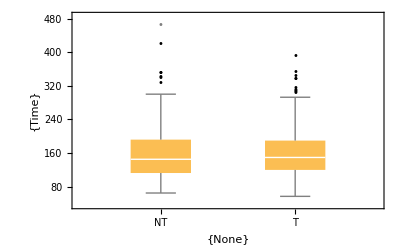

```mathematica
BoxWhiskerChart[{notTimedTime,timedTime},"Outliers",ChartLabels->{{"NT","T"}},AxesLabel->{{None},{"Time"}}] (*Remove great outlier (NOT)timetimed*)
```

```mathematica
MannWhitneyTest[{timedTime,notTimedTime}]
```

0.398226

## Additive:

### Bet Creator:

```mathematica
betSTOP=List[];
stoppluslaag=RandomInteger[{200,200},40]; (*Create uniform gambles*)
stopminlaag=RandomInteger[{-200,-200},40];
stopplushoog=RandomInteger[{500,500},40];
stopminhoog=RandomInteger[{-500,-500},40];
p1=0.5;
p2=0.5;
For[i=1,i≤Length[stoppluslaag],i++,
randomInt1=RandomInteger[{1,2}]; (*Allow for random perturbations on all outcomes around the magnitudes of 200,500*)
randomInt2=RandomInteger[{1,2}];
randomInt3=RandomInteger[{0,5}];
randomInt4=RandomInteger[{0,5}];
a=stoppluslaag[[i]]*If[randomInt1==2,(1+randomInt3/100),(1-randomInt3/100)];
b=stopminlaag[[i]]*If[randomInt2==2,(1+randomInt4/100),(1-randomInt4/100)];
c=stopplushoog[[i]]*If[randomInt1==2,(1+randomInt3/100),(1-randomInt3/100)];
d=a+b-c; (*ensure equal expected value*)
list=List[{p1,a},{1-p1,b},{p2,c},{1-p2,d}];
r1=RandomInteger[{0,1}]; (*Randomise order in bet couples*)
r2=RandomInteger[{0,1}];
AppendTo[betSTOP,{{list[[1+r1]],list[[2-r1]]},{list[[3+r2]],list[[4-r2]]}}]
];
```

### Respondent Data

```mathematica
(*Split the data according to the asisgned starting capital*)
```

### data:

```mathematica
KA =Import["C:\Users\arnev\Documents\Additive Ruin Data CSV.csv"];
KA=ReplaceAll[1->0]/@KA;
KA=ReplaceAll[2->1]/@KA;
KA10K=Select[KA,#[[31]]>3000&][[All,2;;30]];
KA3K=Select[KA,#[[31]]>2000 &&#[[31]]<10000&][[All,2;;30]];
KA1K=Select[KA,#[[31]]<2000 &][[All,2;;30]];
```

### Bayes to generate posterior distributions per bet per starting capital:

```mathematica
n=1;
Posterior=List[];
matrix=Transpose[KA3K]; 
Clear[p];
While[n≤ Length[matrix],
t=1;
prior=List[BetaDistribution[0.5,0.5]];
(*SeedRandom[1234];*)
randy=matrix[[n,All]];
While[t≤Length[matrix[[n,All]]]-Round[0.8*Length[randy]],
If[t==1,updatedprior=bayes[randy[[1;;Round[0.8*Length[randy]]]],PDF[prior[[t]],p]],updatedprior=bayes[{randy[[Round[0.8*Length[randy]]+t-1]]},PDF[prior[[t]],p]]];
AppendTo[prior,updatedprior];
t++;
];
AppendTo[Posterior,Last[prior]];
Print[{n,30}];
n++;
]
```

### Obtained Posteriors and Summary Data

```mathematica
posteriorKA10K="data";
posteriorKA3K="data";
posteriorKA1K="data";
```

```mathematica
listKA1K="data";
listKA3K="data";
listKA10K="data";
```